# Math 223: Homework 1

Maia Powell

28 January 2021

## Problem 1

For this problem, we will be getting familiar with the Series command. We do so by computing various Taylor series of the function (1+x)^(1/x) about the point x=0. Taylor series of degrees 0≤ n ≤ 4 are shown below.

```mathematica
Series[(1+x)^(1/x),{x,0,0}]
```

ⅇ+O[x]^1

```mathematica
Series[(1+x)^(1/x),{x,0,1}]
```

ⅇ-(ⅇ x)/2+O[x]^2

```mathematica
Series[(1+x)^(1/x),{x,0,2}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24+O[x]^3

```mathematica
Series[(1+x)^(1/x),{x,0,3}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+O[x]^4

We now use the Plot command to plot the true function compared to the Taylor series partial sum of degree 4 approximation over the interval [-1,4].

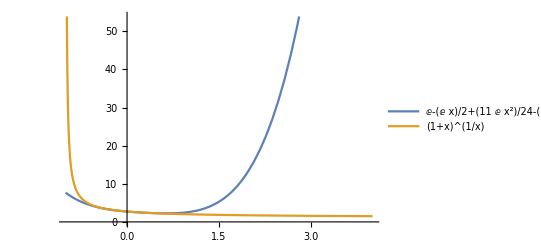

```mathematica
Plot[{Evaluate[Normal[Series[(1+x)^(1/x),{x,0,4}]]], (1+x)^(1/x)},{x,-1,4}, PlotLegends->"Expressions"]
```

## Problem 2

For this problem, we will be getting familiar with the Integrate command. We do so by computing the definite integral of the function sin(x^2) over the interval [0, 3/2].

```mathematica
integ = Integrate[Sin[x^2],{x,0,3/2}]
```

√(π/2) FresnelS[3/(√(2 π))]

Here, we compute the definite integral of the Taylor series partial sum approximation of degree 6 about the point x=0 of the function sin(x^2), again over the interval [0, 3/2].

```mathematica
seri = Integrate[Series[Sin[x^2],{x,0,6}], {x,0,3/2}]
```

1287/1792

We now compare the absolute error between the definite integrals of the true function (sin(x^2)) and the Taylor series approximation of the function using the N command.

```mathematica
N[integ-seri]
```

0.0600458

## Problem 3

For this problem, we will be getting familiar with the DSolve command. We do so by solving εy'' + (1+ε)y' + y = 0 with y(0)=0 and y(1)=e^-1 as boundary values on 0<x<1.

```mathematica
soln = DSolve[{δ *y''[x] + (1+δ )*y'[x] + y[x] == 0, y[0]==0, y[1]==E^(-1)},y[x], {x,0,1}]
```

{{y[x]→(ⅇ^(-(-1+x+x δ)/δ) (-ⅇ^x+ⅇ^(x/δ)))/(-ⅇ+ⅇ^(1/δ))}}

We now plot the solution, and vary values for ε using the Manipulate function.

```mathematica
Manipulate[Plot[{y[x]/.soln/.δ->ϵ},{x,0,1}], {ϵ,0.01,1,Appearance->"Labeled"}]
```

We notice that our solution, no matter the ε value, is always positive (on the interval [0,1]). For ε values close to 0, our solution has a sharp curve; however, as ε→ 1, our solution tends to flatten and smoothen, but becomes undefined at ε=1.